# bivector square and parallelogram figures, Figures for 90 degree rotations. Figure for line intersection. Figure for vector addition, showing scaled multiples of orthonormal bases elements.

### Figures for oriented areas (squares and parallelograms)

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

## bivector square and parallelogram figures.

```mathematica
ClearAll[o, e1, e2, orientedArc, midpoint, midtext, tsub]
o = {0,0};
e2 = {0,1};
e1 = {1,0};

orientedArc[s_, f_, r_,c_] := Module[{data,p},
data=Table[r{Cos[x],Sin[x]},{x,s,f, (f-s)/100}];p=ListPlot[data,Frame->True,Axes->False,Joined->True,PlotStyle->{c,Thick}, AspectRatio->1];
p/.Line[x_]:>{Arrowheads[{0,.05(*,.05*),0}],Arrow[x]}
];

midpoint[p_] := (p[[1]] + p[[2]])/2 ;
midtext[p_, sh_,text_] := Text[text,midpoint[p] + sh]



tsub[t_,s_] := MaTeX["\\mathbf{"<> t<>"}_{"<> s<>"}"]
esub := tsub["e", ToString[#]] &;
```

```mathematica
ClearAll[ bold, sz, fs, shift, sep ]

(*bold = Style[ #, Bold] &;
sz = 14;
fs = Style[ #, FontSize-> sz] &;
tsub[t_,s_] := Subscript[bold[t]// fs,s];
(*esub := tsub[e, #]&;*)
vsub := tsub[v, #]&;*)




shift = -0.06;
sep = 1.5 e1;
```

```mathematica
ClearAll[parallelogram]

(*fixme: use orientedArc here to make the arrow head line up with the curve better*)
parallelogram[v1_,v2_,ori_,l1_,l2_, c1_, c2_, orientation_]:= Module[{m,r},
m = midpoint[{v1,v2}];
r= Min[
Norm[0.7 (m-v1/2)],
Norm[0.7 (m-v2/2)]];
{Thick,c1,
Arrowheads[0.05],Arrow[{{ori,ori+v1},{ori+v1,ori+v1+v2},{ori+v1+v2,ori+v2},{ori+v2,ori}}],
Black,
midtext[{ori,ori+v1},-shift v2,l1],
midtext[{ori+v1,ori+v1+v2},shift v1,l2],
c2,
Circle[
m + ori,
r,
{0,2 Pi 0.9}],
Arrow[{m+ ori +r e2 -orientation shift e1/2,m+ori +r e2+orientation shift e1/2}]
}];
```

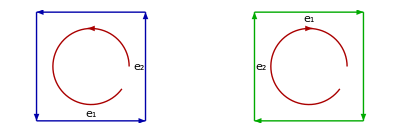

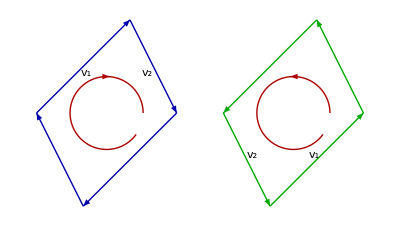

```mathematica
p1 = Graphics[ 
Flatten[
{
parallelogram[e1, e2, o, tsub[e,1], tsub[e,2], Blue//Darker, Red // Darker,1],
parallelogram[e2,e1, 2e1, tsub[e,2], tsub[e,1], Green//Darker, Red // Darker,-1]
}
,1
]]

p2 = Graphics[ 
Flatten[
{
parallelogram[e1+e2, e1/2-e2, o,  tsub[v,1], tsub[v,2], Blue//Darker, Red // Darker,-1],
parallelogram[e1/2-e2,e1+e2, 2e1, tsub[v,2], tsub[v,1], Green//Darker, Red // Darker,1]
}
,1
]]
```

```mathematica
peeters`exportForLatex["orientedAreasFig1", p1]
peeters`exportForLatex["orientedParallelogramFig1", p2]
```

{orientedAreasFig1.eps,orientedAreasFig1pn.png}

{orientedParallelogramFig1.eps,orientedParallelogramFig1pn.png}

### Figures for 90 degree rotations.

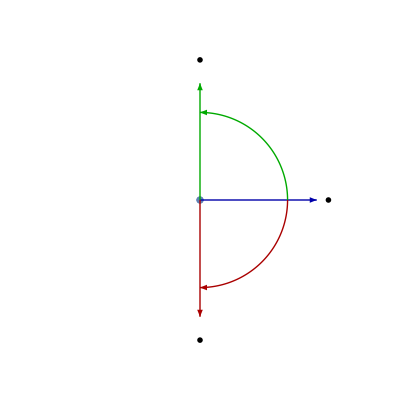

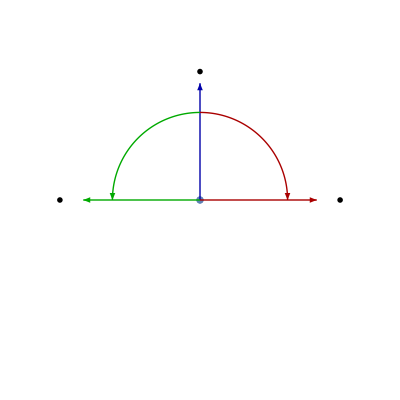

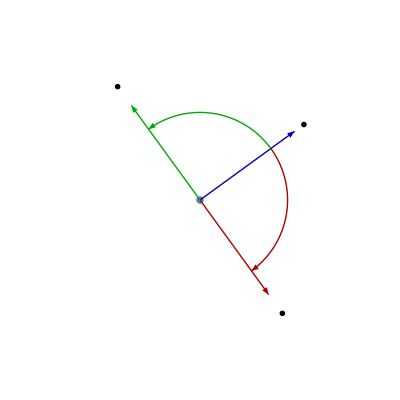

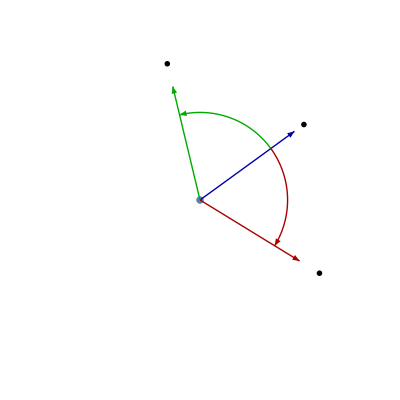

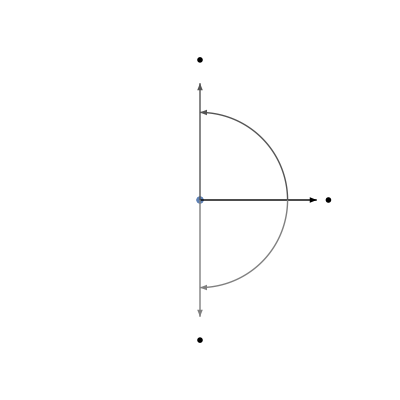

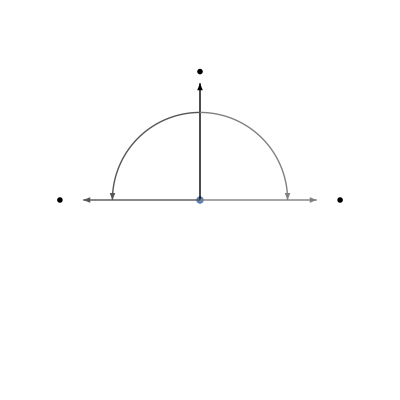

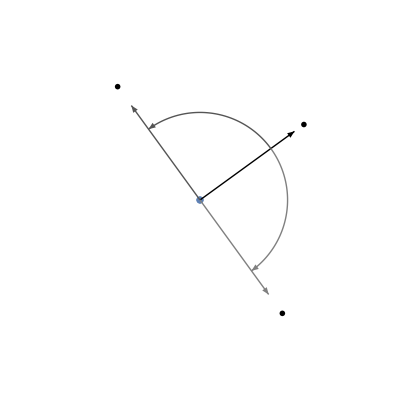

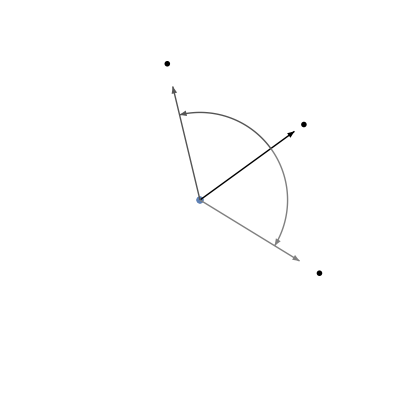

```mathematica
rotatedVectorPlot[rn_,th_,th2_,l1_, l2_, l3_, c1_, c2_, c3_] := Module[{ v1, v2, v0},

v1 = e1 Cos[th] + e2 Sin[th];
v2 = e1 Cos[th + th2] + e2 Sin[th +th2];
v0 = e1 Cos[th - th2] + e2 Sin[th -th2];
Show[
ListPlot[{o}, AspectRatio->1, PlotRange->{{-rn,rn},{-rn, rn}}, Ticks -> None, Axes -> None],
Graphics[
{
Thick,c1,
Arrowheads[0.05],
Arrow[{o, v1}],
c2,
Arrow[{o, v2}],
c3,
Arrow[{o, v0}],
Black,
Text[l1// MaTeX,v1*1.1],
Text[l2// MaTeX,v2*1.2],
Text[l3// MaTeX,v0*1.2]
}
] (*Graphics*),
orientedArc[ th,th+th2, 0.75, c2],
orientedArc[th, th-th2,0.75, c3]
]
]


p3 =rotatedVectorPlot[1.4,0,Pi/2,"\\mathbf{e}_1", "\\mathbf{e}_1 i", "i \\mathbf{e}_1", Blue//Darker, Green//Darker, Red//Darker]
p4 =rotatedVectorPlot[1.4,Pi/2,Pi/2,"\\mathbf{e}_2", "\\mathbf{e}_2 i", "i \\mathbf{e}_2", Blue//Darker, Green//Darker, Red//Darker]
p5 =rotatedVectorPlot[1.4,Pi/5,Pi/2,"\\mathbf{x}", "\\mathbf{x} i", "i \\mathbf{x}", Blue//Darker, Green//Darker, Red//Darker]
p6 =rotatedVectorPlot[1.4,Pi/5,3Pi/8,"\\mathbf{x}", "\\mathbf{x} e^{i\\theta}", " e^{i\\theta} \\mathbf{x}", Blue//Darker, Green//Darker, Red//Darker]

p3b =rotatedVectorPlot[1.4,0,Pi/2,"\\mathbf{e}_1", "\\mathbf{e}_1 i", "i \\mathbf{e}_1", Black, Gray//Darker, Gray]
p4b =rotatedVectorPlot[1.4,Pi/2,Pi/2,"\\mathbf{e}_2", "\\mathbf{e}_2 i", "i \\mathbf{e}_2", Black, Gray//Darker, Gray]
p5b =rotatedVectorPlot[1.4,Pi/5,Pi/2,"\\mathbf{x}", "\\mathbf{x} i", "i \\mathbf{x}", Black, Gray//Darker, Gray]
p6b =rotatedVectorPlot[1.4,Pi/5,3Pi/8,"\\mathbf{x}", "\\mathbf{x} e^{i\\theta}", " e^{i\\theta} \\mathbf{x}", Black, Gray//Darker, Gray]
```

```mathematica
peeters`exportForLatex["color/rotationOfe1Fig1", p3]
peeters`exportForLatex["color/rotationOfe2Fig1", p4]
peeters`exportForLatex["color/rotationOfVFig1", p5]
peeters`exportForLatex["color/rotationOfXFig1", p6]

peeters`exportForLatex["bw/rotationOfe1Fig1", p3b]
peeters`exportForLatex["bw/rotationOfe2Fig1", p4b]
peeters`exportForLatex["bw/rotationOfVFig1", p5b]
peeters`exportForLatex["bw/rotationOfXFig1", p6b]
```

{color/rotationOfe1Fig1.eps,color/rotationOfe1Fig1pn.png}

{color/rotationOfe2Fig1.eps,color/rotationOfe2Fig1pn.png}

{color/rotationOfVFig1.eps,color/rotationOfVFig1pn.png}

{color/rotationOfXFig1.eps,color/rotationOfXFig1pn.png}

{bw/rotationOfe1Fig1.eps,bw/rotationOfe1Fig1pn.png}

{bw/rotationOfe2Fig1.eps,bw/rotationOfe2Fig1pn.png}

{bw/rotationOfVFig1.eps,bw/rotationOfVFig1pn.png}

{bw/rotationOfXFig1.eps,bw/rotationOfXFig1pn.png}

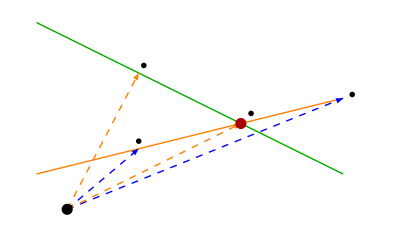

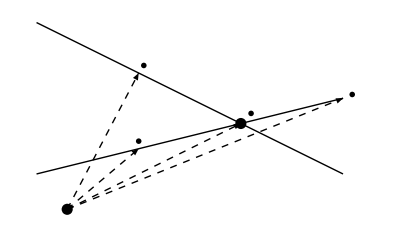

```mathematica
ClearAll[ps, intersectionOfLinesFig1, bwintersectionOfLinesFig1]
ps[c1_, c2_, c3_, c4_, c5_] :=Module[{f,g, a0, a1, b0, b1,inter, p, tval,oo},
f = #/2 + 1 &;
g = -# +4 &;
a0 = {1,f[1]};
a1 = {3,f[3]};
b0 = {1,g[1]};
b1 = {2,g[2]};
oo = {0.3,0.3};
inter = Solve[ a0 + s(a1-a0) == b0 + t(b1-b0),{s,t}];
tval = (t/.inter // Flatten)// First;
p = b0 + tval(b1-b0);
Show[
(*Plot[{f[x], g[x]},{x,0,3}, PlotRange->{{0,3.2},{0,4}}, Ticks -> None, PlotStyle->{Thick}, Axes -> False],*)
Plot[f[x],{x,0,3}, PlotRange->{{0,3.2},{0,4}}, Ticks -> None, PlotStyle->{Thick, c4}, Axes -> False],
Plot[g[x],{x,0,3}, PlotRange->{{0,3.2},{0,4}}, Ticks -> None, PlotStyle->{Thick, c5}, Axes -> False],
Graphics[
{
c1 ,
Thick,
,Dashed
,Arrowheads[0.03]
,Arrow[{oo,a0}]
,Arrow[{oo,a1}]
,c2 
,Arrow[{oo,b0}]
,Arrow[{oo,b1}]
,Black
, Text[ tsub["a","0"], a0*1.1-0.1e1]
, Text[ tsub["a","1"], a1*1.03]
, Text[ tsub["b","0"], b0*1.05]
, Text[ tsub["b","1"], b1*1.05+0.1e2]
, c3
, PointSize[0.02]
, Point[ p ]
,Black,
, Point[ oo ]
}
] (*Graphics*)
] (*Show*) 

]

intersectionOfLinesFig1= ps[Blue,Orange, Red // Darker, Orange, Green// Darker]
bwintersectionOfLinesFig1= ps[Black,Black, Black, Black, Black]
```

```mathematica
peeters`exportForLatex["color/intersectionOfLinesFig1", intersectionOfLinesFig1]
peeters`exportForLatex["bw/intersectionOfLinesFig1", bwintersectionOfLinesFig1]
```

{color/intersectionOfLinesFig1.eps,color/intersectionOfLinesFig1pn.png}

{bw/intersectionOfLinesFig1.eps,bw/intersectionOfLinesFig1pn.png}

Figure for vector addition, showing scaled multiples of orthonormal bases elements.

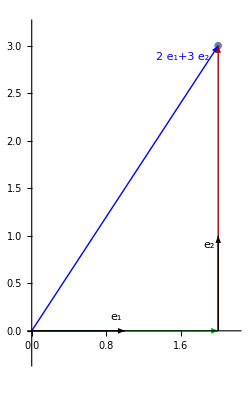

```mathematica
ClearAll[ps2]
ps2 =Module[{v,vx,vy,nv,tplace},
v = {2,3};
nv = Norm[v];
vx = v.e1 e1;
vy = v.e2 e2;
tplace = 0.9;

Show[
ListPlot[{v}, PlotRange->{{0, v.e1 + 0.2},{-0.3,v.e2 + 0.2}},AspectRatio->Full ],
Graphics[
{
Blue ,
Thick,
,Arrowheads[0.05]
,Arrow[{o,v}]
, Text[ (v.e1 // fs) tsub[e,1] + (v.e2 // fs ) tsub[e,2], tplace v + nv (e2-e1)/20]
,Green // Darker
,Arrow[{o,vx}]
, Red // Darker
,Arrow[{vx, v}]
, Black
,Arrow[{vx ,vx +e2}]
,Arrow[{o,e1}]
, Text[ tsub[e,1], tplace e1+ vy/20]
, Text[ tsub[e,2], tplace (vx +e2)+vx/20]
}
] (*Graphics*)
] (*Show*) 
] (* Module *)
```

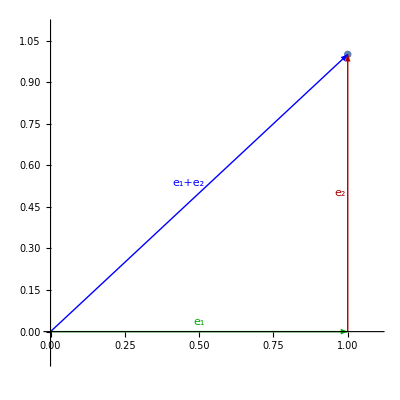

```mathematica
ClearAll[ps3]
ps3 =Module[{v,vx,vy,nv,tplace,sp},
v = {1,1};
nv = Norm[v];
vx = v.e1 e1;
vy = v.e2 e2;
tplace = 0.9;
sp = 0.1;

Show[
ListPlot[{v}, PlotRange->{{0, v.e1 + sp},{-sp ,v.e2 + sp}},AspectRatio->1 , Ticks ->None],
Graphics[
{
Thick,
Arrowheads[0.05]

,Blue 
,Arrow[{o,v}]
,Text[ tsub[e,1] +  tsub[e,2], v/2 + nv (e2-e1)/40]

,Green // Darker
,Arrow[{o,vx}]
,Text[tsub[e,1] , e1/2 + e2/30]

,Red // Darker
,Arrow[{vx, v}]
,Text[tsub[e,2], e1 + e2/2 - e1/40]
}
] (*Graphics*)
] (*Show*) 
] (* Module *)
```

```mathematica
peeters`exportForLatex["unitSumFig1", ps3]
```

{unitSumFig1.eps,unitSumFig1pn.png}

```mathematica
ClearAll[ps4, ps4f, ps4b]

ps4f[c1_, c2_, c3_] :=Module[{v,vx,vy,nv,tplace,sp, tu, tv},
v = {2,3};
vx = v.e1 e1;
vy = v.e2 e2;
tplace = 0.9;
sp = 0.1;
tu = "u" // MaTeX;
tv = "v" // MaTeX;

Show[
ListPlot[{v}, 
PlotRange->{{0, v.e1 + sp},{-sp ,v.e2 + sp}},
AspectRatio->3/2 , 
Ticks ->None,
Axes -> None,
PlotStyle->{c1,PointSize[Large]}
 
]
,
Graphics[
{
Thick,
Arrowheads[0.05]

,c1 
,Arrow[{o,v}]
,Text[ Row[{tu, "+"// MaTeX, tv}], v/2 + 0.15 Normalize[ e2-e1]]

,c2
,Arrow[{o,vx}]
,Text[tu , vx/2+ 0.1 e2],

,c3
,Arrow[{vx, v}]
,Text[tv, vx + vy/2 - 0.1 e1]
}
] (*Graphics*)
] (*Show*) 
] (* Module *)

ps4 = ps4f[Blue, Green// Darker, Red//Darker]
ps4b = ps4f[Black, Black,Black]
```

-Graphics-

-Graphics-

```mathematica
peeters`exportForLatex["color/unitSumFig1", ps4]
```

{color/unitSumFig1.eps,color/unitSumFig1pn.png}

{bw/unitSumFig1.eps,bw/unitSumFig1pn.png}

```mathematica
peeters`exportForLatex["bw/unitSumFig1", ps4b]
```

{bw/unitSumFig1.eps,bw/unitSumFig1pn.png}

```mathematica
tsub["a",0]
```

StringJoin::string: String expected at position 2 in \mathbf{a}_{<>0<>}.

-Graphics-